# Investigating the relationship between Gini index and well-being along the US

Neofytos Themistokleous

## Introduction

Inspired by the work of social epidemiologist Richard Wilkinson, I decided to try and replicate some of his results using the Wolfram Language. 

More specifically, Richard has found the Gini index for an area to be inversely proportional to quantities of social wellbeing.  ["Click Here to Watch the Video"](https://www.youtube.com/watch?v=aOUJbV66Nm4) of him explaining his claims.  First things first. What is the Gini index? Let’ s ask the Wolfram Language :

```mathematica
EntityValue[EntityProperty["AdministrativeDivision","GiniIndex"],"Definition"]
```

The extent to which the distribution of income among individuals or households within an economy deviates from a perfectly equal distribution. A Lorenz curve plots the cumulative percentages of total income received against the cumulative number of recipients, starting with the poorest individual or household. The Gini index measures the area between the Lorenz curve and a hypothetical line of absolute equality, expressed as a fraction of the maximum area under the line. Thus a Gini index of 0 represents perfect equality, while an index of 1 implies perfect inequality.

So, simply put, it is the measurement of the population’s income inequality in an area.

## Implementation Decisions

Since, the “AdministrativeDivision” entity in the Wolfram Language provides a lot of data for the US states, it was decided to explore the correlation of “Gini index” with a number of entities that are linked to social wellbeing for all the US States.

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
RandomSample[usstates,5]
```

{Connecticut, United States,Pennsylvania, United States,Oregon, United States,Vermont, United States,Washington, United States}

Now, how does one measure social wellbeing? The "AdministrativeDivision" entity contains plenty of categories. To see them:

```mathematica
EntityProperties["AdministrativeDivision"];
```

A number of categories from that list were chosen, based on Richard Wilkinson’s claims and my own intuition.

```mathematica
allentities = {EntityProperty["AdministrativeDivision","GiniIndex"],EntityProperty["AdministrativeDivision","Population"],EntityProperty["AdministrativeDivision","Businesses"],EntityProperty["AdministrativeDivision","CrimeRate"],EntityProperty["AdministrativeDivision","DisabledPersons"],EntityProperty["AdministrativeDivision","AnnualDeaths"],EntityProperty["AdministrativeDivision","HealthInsuranceUncoveredRate"],EntityProperty["AdministrativeDivision","HomeOwnershipRate"],EntityProperty["AdministrativeDivision","MinimumWage"],EntityProperty["AdministrativeDivision","TotalVotingRate"],EntityProperty["AdministrativeDivision","CivilianUnemploymentRate"]} ;
```

A list of names for those quantities in order to select them from the dataset, further down the road.

## Acquiring & preparing the data

It is about time to get the data. Since the EntityValue function is listable, it is able to requests the value of all categories for all the US States. QuantityMagnitude strips the quantities off their units, while Thread and AssociationThread allows mapping of all the keys with the data at once.

```mathematica
data= QuantityMagnitude[EntityValue[usstates,allentities,"PropertyEntityAssociation"]];
```

Some of the selected variables : number of businesses, disabled people, and annual deaths are not normalised. To normalised them :

```mathematica
normalizeByPop[key_]:=Function[Append[#,key->#[key]/#[EntityProperty["AdministrativeDivision","Population"]]]];
```

```mathematica
data=normalizeByPop[EntityProperty["AdministrativeDivision","Businesses"]]@data;
```

```mathematica
data=normalizeByPop[EntityProperty["AdministrativeDivision","DisabledPersons"]]@data;
```

```mathematica
data=normalizeByPop[EntityProperty["AdministrativeDivision","AnnualDeaths"]]@data;
```

Let' s have a look the result in a dataset :

```mathematica
data//Dataset
```

Dataset[<>]

## Data analysis & Visualisation

With the data in the appropriate format, it is about time to do some investigations.

If only there existed a simple command, allowing us to have a visual idea of how much the Gini index varies across the US.

```mathematica
GeoRegionValuePlot[data[EntityProperty["AdministrativeDivision","GiniIndex"]]]
```

-Graphics-

Some patterns can be spotted, for example higher Gini index for the states in the east of the country. What about the rest of our variables? for example unemployment rate:

```mathematica
GeoRegionValuePlot[data[EntityProperty["AdministrativeDivision","CivilianUnemploymentRate"]]]
```

-Graphics-

It  seems more random that gini index. Maybe it is time to quantify our analysis. First  perform a fit between Gini index and all the other quantities individually :

```mathematica
fits= Table[Fit[Transpose@{Values@data[EntityProperty["AdministrativeDivision","GiniIndex"]],Values@data[allentities[[i]]]},{1,x},x],{i,2,Length[allentities]}];
```

```mathematica
fits
```

{-9.45956×10^7+2.18128×10^8 x,0.136167-0.107738 x,-0.0101126+0.0803031 x,-0.184755+0.733476 x,0.00281994+0.0130913 x,-8.28973+48.5082 x,131.776-139.812 x,1.72733+14.9412 x,126.574-146.345 x,-5.617+19.8736 x}

Let’s plot the fitted lines, together with the scatter plots, to check if they agree.

```mathematica
plots=ArrayReshape[
Table[
Show[
ListPlot[Transpose@{Values@data[EntityProperty["AdministrativeDivision","GiniIndex"]],Values@data[allentities[[i]]]},AxesLabel->{"Gini index",CommonName[allentities[[i]]]}],
Plot[fits[[i-1]],{x,0.425,0.55}]]
,{i,2,Length[allentities]}]
,{4,3}];
```

```mathematica
GraphicsGrid[plots,ImageSize->{1200,1200}]
```

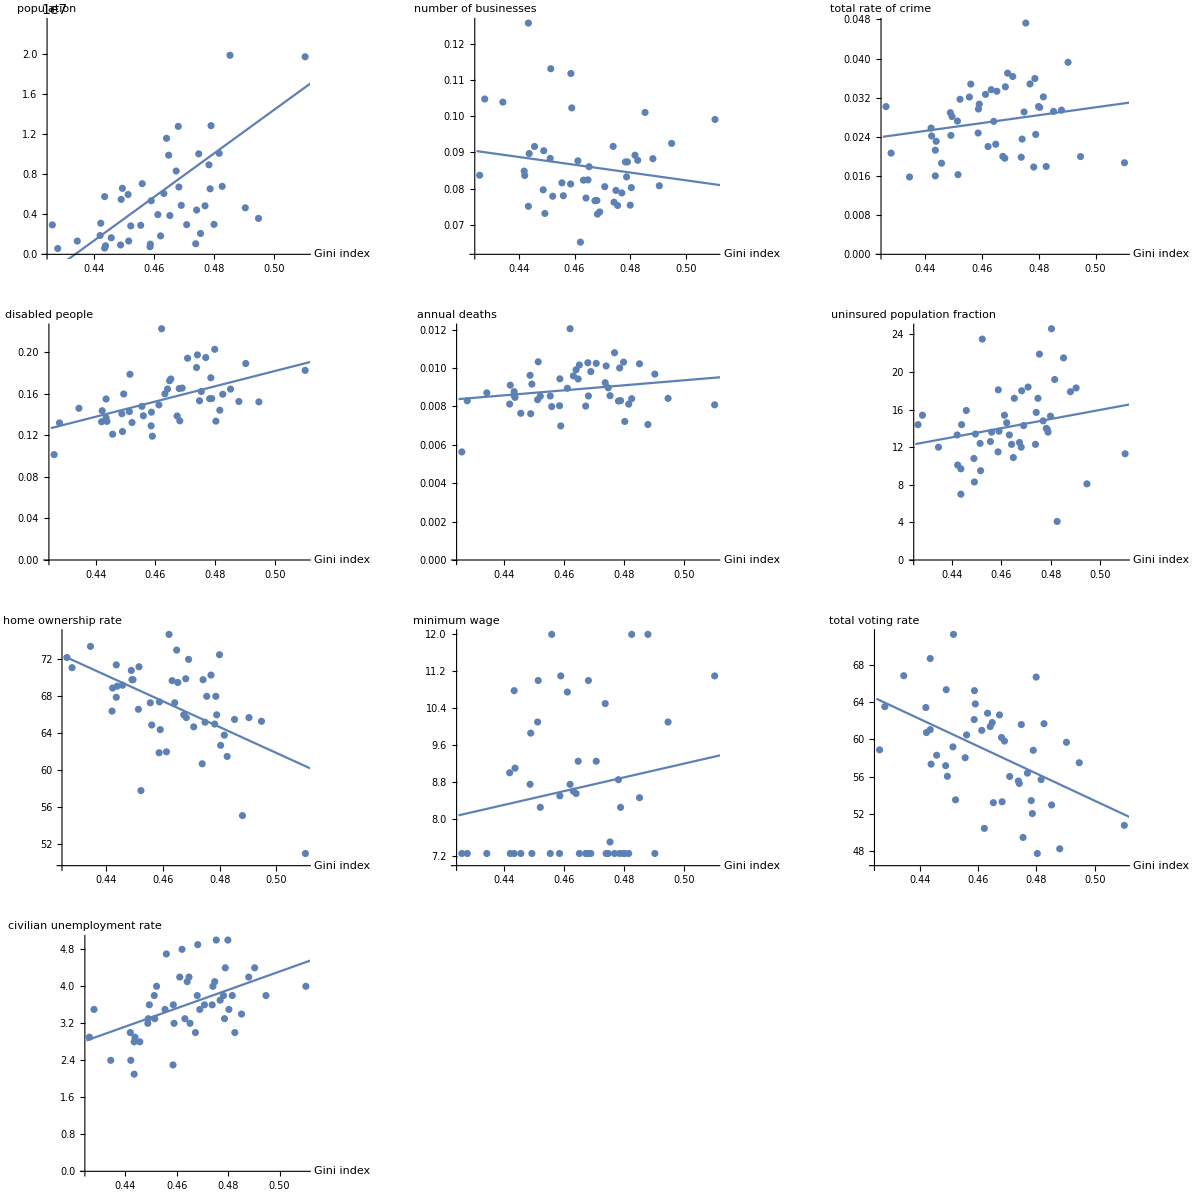

Some correlations can be inferred from the plots, but is there a way to go a step further? We can use the Correlation function which returns the Pearson’ s correlation coefficient between two vectors.

```mathematica
correlations=Reverse@SortBy[Abs[#[[3]]]&]@Table[{EntityProperty["AdministrativeDivision","GiniIndex"],allentities[[i]],Correlation[Values@data[EntityProperty["AdministrativeDivision","GiniIndex"]],Values@data[allentities[[i]]]]},{i,2,Length[allentities]}];
```

Then it is possible to sort the quantities based on their correlation to the Gini index:

```mathematica
correlations//Column
```

{Gini index,population,0.53733}
{Gini index,home ownership rate,-0.532003}
{Gini index,disabled people,0.529797}
{Gini index,civilian unemployment rate,0.506169}
{Gini index,total voting rate,-0.485893}
{Gini index,uninsured population fraction,0.210305}
{Gini index,total rate of crime,0.203853}
{Gini index,annual deaths,0.202066}
{Gini index,minimum wage,0.167087}
{Gini index,number of businesses,-0.16282}

## Conclusions

The biggest correlation comes from population, which doesn’t say much, but the next instances:  home ownership, disabled people, unemployment rate tend to agree with my initial proposal. Correlations appear to be a lot less drastic that Richard Wilkinson suggested, although this is expected considering the simplicity of the current analysis. 

If Administrative Division data existed for US sub-regions or for other countries, a more thorough analysis could have been performed. Also,  it would really help if more quantities were included; for example: violence, homicide rates, teenage birth rates, mental health, people in prison, child well-being, life expectancy, gun ownership and suicide rates.

## References:

Richard Wilkinson’s claims: https://www.youtube.com/watch?v=aOUJbV66Nm4

Access Detailed US Census Data: http://www.wolfram.com/language/12/financial-and-socioeconomic-entities/access-detailed-us-census-data.html?product=mathematica

Travel All Capitals of the Conterminous US States: https://www.wolfram.com/language/11/geo-computation/travel-all-capitals-of-the-conterminous-us-states.html?product=language